```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY196/sec_int_data/368nm.dat"]
```

{{1.64105,-0.883049},{1.57964,-0.866644},{1.51907,-0.784912},{1.47433,-0.765933},{1.70936,-0.899065},{1.78557,-0.936544}}

0.028036-0.546334 x

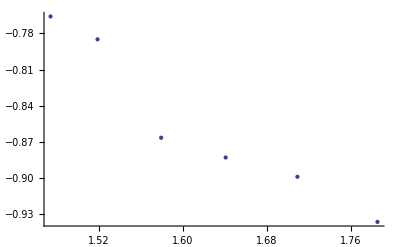

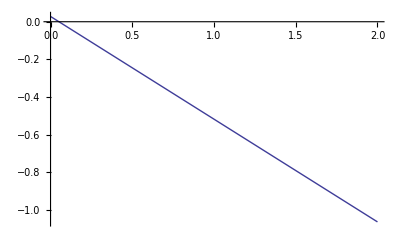

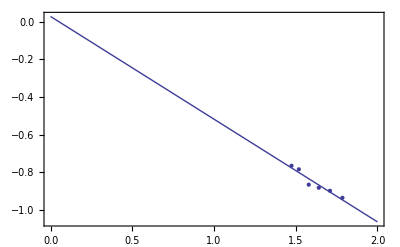

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```